```mathematica
ArrayPlot[
Table[Reverse[IntegerDigits[i,3,5]],{i,0,3^3}]
]
```

-Graphics-

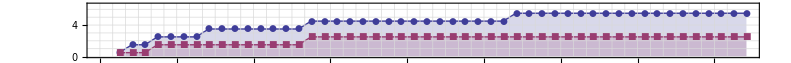

```mathematica
With[
{max=50,p=2},
ListLinePlot[{Table[{n+1/2,Floor[Log[p,n]+1]-1/2},{n,0,max}],Table[{n+1/2,Floor[Log[p,n]/2+1]-1/2},{n,0,max}]},
PlotRange->{Automatic,{0,1+Log[p,max]}},
Filling->Axis,
GridLines->{Table[i,{i,0,max}], {0,1,2,3,4,5,6}},
PlotMarkers->Automatic,
AspectRatio->2*p/max,
Frame->True
]
]
```

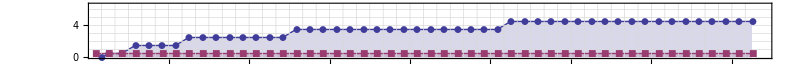

```mathematica
With[
{max=50,p=2},
ListLinePlot[{Table[{n-1/2,Floor[Log2[n]]-1/2},{n,1,max}],Table[{n-1/2,1/2},{n,1,max}]},
PlotRange->{{1,max},{0,1+Log[p,max]}},
Filling->Axis,
GridLines->{Table[i,{i,0,max}], {0,1,2,3,4,5,6}},
PlotMarkers->Automatic,
FrameTicks->All,
AspectRatio->2*p/max,
Frame->True
]
]
```